# For Gianluca

```mathematica
ll=Tuples[{0,1},4]
```

```mathematica
Sum[E^(-(I*Pi)/d*Sum[(ll[[j1,k]]+ll[[j2,k]]+ll[[j3,k]]+ll[[j4,k]]),{k,1,Length[ll[[1]]]}])*Product[Cos[(Pi*(ll[[j1,i]]+ll[[j2,i]]+ll[[j3,i]]+ll[[j4,i]]))/d],{i,1,Length[ll[[1]]]}],{j1,1,Length[ll]},{j2,1,Length[ll]},{j3,1,Length[ll]},{j4,1,Length[ll]}]//Simplify
```

```mathematica
Sum[Product[1+E^((-2*Pi*I)/d*(ll[[j1,i]]+ll[[j2,i]]+ll[[j3,i]]+ll[[j4,i]])),{i,1,Length[ll[[1]]]}],{j1,1,Length[ll]},{j2,1,Length[ll]},{j3,1,Length[ll]},{j4,1,Length[ll]}]//Simplify
```

# Analytic calculations checks

## A checks - output checking

Lets define first the

```mathematica
(* Mathematica has internat function to generate a discrete Fourier transform matrix *)
UFT1 = FourierMatrix[2];
UFT2 = FourierMatrix[4];
```

```mathematica
UFT1//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
UFT2//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | ⅈ/2 | -1/2 | -ⅈ/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -ⅈ/2 | -1/2 | ⅈ/2)

Lets define the Q operator

```mathematica
(* Generated by the 4 Pauli strings on 1 qubit but taken to 4 times replicated space *)
PauliString1[i_]:=PauliMatrix[i];
Q1=(1/4)*Sum[KroneckerProduct[PauliString1[i],PauliString1[i],PauliString1[i],PauliString1[i]],{i,0,3}];

(* Generated by the 16 Pauli strings on 2 qubits but taken to 4 times replicated space *)
PauliString2[i_,j_]:=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]];
Q2=(1/16)*Sum[KroneckerProduct[PauliString2[i,j],PauliString2[i,j],PauliString2[i,j],PauliString2[i,j]],{i,0,3},{j,0,3}];

(* Generated by the 16 Pauli strings on 2 qubits but taken to 4 times replicated space *)
PauliString3[i_,j_,k_]:=KroneckerProduct[SparseArray[PauliMatrix[i]],SparseArray[PauliMatrix[j]],SparseArray[PauliMatrix[k]]];
Q3=(1/64)*Sum[KroneckerProduct[PauliString3[i,j,k],PauliString3[i,j,k],PauliString3[i,j,k],PauliString3[i,j,k]],{i,0,3},{j,0,3},{k,0,3}];
```

```mathematica
MatrixPlot[Q1,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
MatrixPlot[Q2,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
MatrixPlot[Q3,PlotTheme->"Detailed"]
```

-Graphics-

Lets define the Permutation operator \Pi_sim

```mathematica
(* function to generate the pertunations *)
indexToQubitIndices[n_,numQubits_]:=PadLeft[IntegerDigits[n-1,2],numQubits];
permutationMatrix[permutation_]:=With[{numQubits=Length@permutation},SparseArray[{{i_,j_}:>1/;Equal[Permute[indexToQubitIndices[i,numQubits],permutation],indexToQubitIndices[j,numQubits]]},2^numQubits {1,1}]];

(* list the possible permutations of 1 qubit on 4 times replicated space *)
permsingle=Permutations@{1,2,3,4};

(* total operator reads *)
P1=(1/24)*Sum[permutationMatrix[Flatten[permsingle[[i]]]],{i,1,24}];

(* list the possible permutations of 2 qubits on 4 times replicated space *)
permdouble=Permutations@{{1,2},{3,4},{5,6},{7,8}};

(* total operator reads *)
P2=(1/24)*Sum[permutationMatrix[Flatten[permdouble[[i]]]],{i,1,24}];
(*
permtriple=Permutations@{{1,2,3},{4,5,6},{7,8,9},{10,11,12}};

P3=(1/24)*Sum[permutationMatrix[Flatten[permtriple[[i]]]],{i,1,24}];
*)
```

```mathematica
P1
```

SparseArray[…]

```mathematica
P2
```

SparseArray[…]

```mathematica
MatrixPlot[P1,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
MatrixPlot[P2,PlotTheme->"Detailed"]
```

-Graphics-

### Evaluation for 1 qubit

```mathematica
A1N1=Tr[ KroneckerProduct[ConjugateTranspose[UFT1],ConjugateTranspose[UFT1],ConjugateTranspose[UFT1],ConjugateTranspose[UFT1]].Q1.KroneckerProduct[UFT1,UFT1,UFT1,UFT1].Q1.P1]
```

2

```mathematica
A2N1=
Tr[ KroneckerProduct[ConjugateTranspose[UFT1],ConjugateTranspose[UFT1],ConjugateTranspose[UFT1],ConjugateTranspose[UFT1]].Q1.KroneckerProduct[UFT1,UFT1,UFT1,UFT1].P1]
```

2

### Evaluation for 2 qubit

```mathematica
A1N2=Tr[ KroneckerProduct[ConjugateTranspose[UFT2],ConjugateTranspose[UFT2],ConjugateTranspose[UFT2],ConjugateTranspose[UFT2]].Q2.KroneckerProduct[UFT2,UFT2,UFT2,UFT2].Q2.P2]
```

2

```mathematica
A2N2=
Tr[ KroneckerProduct[ConjugateTranspose[UFT2],ConjugateTranspose[UFT2],ConjugateTranspose[UFT2],ConjugateTranspose[UFT2]].Q2.KroneckerProduct[UFT2,UFT2,UFT2,UFT2].P2]
```

5

Linear magic expression

```mathematica
Mlin[d_,a_,b_]:=1-d*(6/((d+1)*(d+2)*(d+4))*a+24/(d*(d+1)*(d+2)*(d+4))*b);
```

```mathematica
Mlin[2,A1N1,A2N1]
```

0

```mathematica
Mlin[4,A1N2,A2N2]
```

3/10

```mathematica
f[k1_,k1p_,k2_,k2p_]:=E^((-I*Pi)/2*(k1*k1p+k2*k2p))+E^((-I*Pi)/2*(k1*k1p+Mod[k2+1,2]*k2p))+E^((-I*Pi)/2*(Mod[k1+1,2]*k1p+k2*k2p))+E^((-I*Pi)/2*(Mod[k1+1,2]*k1p+Mod[k2+1,2]*k2p));
```

```mathematica
t=Table[{f[k1,k1p,k2,k2p]},{k1,0,1},{k2,0,1}]//FullSimplify//MatrixForm
```

((1+ⅇ^(-1/2 ⅈ k1p π)+ⅇ^(-1/2 ⅈ k2p π)+ⅇ^(-1/2 ⅈ (k1p+k2p) π)) | (1+ⅇ^(-1/2 ⅈ k1p π)+ⅇ^(-1/2 ⅈ k2p π)+ⅇ^(-1/2 ⅈ (k1p+k2p) π))
(1+ⅇ^(-1/2 ⅈ k1p π)+ⅇ^(-1/2 ⅈ k2p π)+ⅇ^(-1/2 ⅈ (k1p+k2p) π)) | (1+ⅇ^(-1/2 ⅈ k1p π)+ⅇ^(-1/2 ⅈ k2p π)+ⅇ^(-1/2 ⅈ (k1p+k2p) π)))

```mathematica
ll=Tuples[{0,1},4]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

```mathematica
Mod[ll[[7]]+ll[[8]],2]
```

{0,0,1}

```mathematica
f[k1_,k3_]:=Sum[E^(-(2*Pi*I)/2^Length[ll[[1]]]*(Mod[ll[[k1]]+ll[[k2]],2].ll[[k3]])),{k2,1,Length[ll]}];
```

```mathematica
Table[f[k1,k3],{k1,1,Length[ll]},{k3,1,Length[ll]}]//MatrixForm
```

(8 | 4+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)
8 | 4+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)
8 | 4+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)
8 | 4+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)
8 | 4+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)
8 | 4+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)
8 | 4+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)
8 | 4+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | 4+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4) | (1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4))

```mathematica
Table[{ll[[k1]],ll[[k3]],f[k1,k3]},{k1,1,Length[ll]},{k3,1,Length[ll]}]
```

{{{{0,0,0,0},{0,0,0,0},16},{{0,0,0,0},{0,0,0,1},8-8 ⅈ},{{0,0,0,0},{0,0,1,0},8-8 ⅈ},{{0,0,0,0},{0,0,1,1},-8 ⅈ},{{0,0,0,0},{0,1,0,0},8-8 ⅈ},{{0,0,0,0},{0,1,0,1},-8 ⅈ},{{0,0,0,0},{0,1,1,0},-8 ⅈ},{{0,0,0,0},{0,1,1,1},-4-4 ⅈ},{{0,0,0,0},{1,0,0,0},8-8 ⅈ},{{0,0,0,0},{1,0,0,1},-8 ⅈ},{{0,0,0,0},{1,0,1,0},-8 ⅈ},{{0,0,0,0},{1,0,1,1},-4-4 ⅈ},{{0,0,0,0},{1,1,0,0},-8 ⅈ},{{0,0,0,0},{1,1,0,1},-4-4 ⅈ},{{0,0,0,0},{1,1,1,0},-4-4 ⅈ},{{0,0,0,0},{1,1,1,1},-4}},{{{0,0,0,1},{0,0,0,0},16},{{0,0,0,1},{0,0,0,1},8-8 ⅈ},{{0,0,0,1},{0,0,1,0},8-8 ⅈ},{{0,0,0,1},{0,0,1,1},-8 ⅈ},{{0,0,0,1},{0,1,0,0},8-8 ⅈ},{{0,0,0,1},{0,1,0,1},-8 ⅈ},{{0,0,0,1},{0,1,1,0},-8 ⅈ},{{0,0,0,1},{0,1,1,1},-4-4 ⅈ},{{0,0,0,1},{1,0,0,0},8-8 ⅈ},{{0,0,0,1},{1,0,0,1},-8 ⅈ},{{0,0,0,1},{1,0,1,0},-8 ⅈ},{{0,0,0,1},{1,0,1,1},-4-4 ⅈ},{{0,0,0,1},{1,1,0,0},-8 ⅈ},{{0,0,0,1},{1,1,0,1},-4-4 ⅈ},{{0,0,0,1},{1,1,1,0},-4-4 ⅈ},{{0,0,0,1},{1,1,1,1},-4}},{{{0,0,1,0},{0,0,0,0},16},{{0,0,1,0},{0,0,0,1},8-8 ⅈ},{{0,0,1,0},{0,0,1,0},8-8 ⅈ},{{0,0,1,0},{0,0,1,1},-8 ⅈ},{{0,0,1,0},{0,1,0,0},8-8 ⅈ},{{0,0,1,0},{0,1,0,1},-8 ⅈ},{{0,0,1,0},{0,1,1,0},-8 ⅈ},{{0,0,1,0},{0,1,1,1},-4-4 ⅈ},{{0,0,1,0},{1,0,0,0},8-8 ⅈ},{{0,0,1,0},{1,0,0,1},-8 ⅈ},{{0,0,1,0},{1,0,1,0},-8 ⅈ},{{0,0,1,0},{1,0,1,1},-4-4 ⅈ},{{0,0,1,0},{1,1,0,0},-8 ⅈ},{{0,0,1,0},{1,1,0,1},-4-4 ⅈ},{{0,0,1,0},{1,1,1,0},-4-4 ⅈ},{{0,0,1,0},{1,1,1,1},-4}},{{{0,0,1,1},{0,0,0,0},16},{{0,0,1,1},{0,0,0,1},8-8 ⅈ},{{0,0,1,1},{0,0,1,0},8-8 ⅈ},{{0,0,1,1},{0,0,1,1},-8 ⅈ},{{0,0,1,1},{0,1,0,0},8-8 ⅈ},{{0,0,1,1},{0,1,0,1},-8 ⅈ},{{0,0,1,1},{0,1,1,0},-8 ⅈ},{{0,0,1,1},{0,1,1,1},-4-4 ⅈ},{{0,0,1,1},{1,0,0,0},8-8 ⅈ},{{0,0,1,1},{1,0,0,1},-8 ⅈ},{{0,0,1,1},{1,0,1,0},-8 ⅈ},{{0,0,1,1},{1,0,1,1},-4-4 ⅈ},{{0,0,1,1},{1,1,0,0},-8 ⅈ},{{0,0,1,1},{1,1,0,1},-4-4 ⅈ},{{0,0,1,1},{1,1,1,0},-4-4 ⅈ},{{0,0,1,1},{1,1,1,1},-4}},{{{0,1,0,0},{0,0,0,0},16},{{0,1,0,0},{0,0,0,1},8-8 ⅈ},{{0,1,0,0},{0,0,1,0},8-8 ⅈ},{{0,1,0,0},{0,0,1,1},-8 ⅈ},{{0,1,0,0},{0,1,0,0},8-8 ⅈ},{{0,1,0,0},{0,1,0,1},-8 ⅈ},{{0,1,0,0},{0,1,1,0},-8 ⅈ},{{0,1,0,0},{0,1,1,1},-4-4 ⅈ},{{0,1,0,0},{1,0,0,0},8-8 ⅈ},{{0,1,0,0},{1,0,0,1},-8 ⅈ},{{0,1,0,0},{1,0,1,0},-8 ⅈ},{{0,1,0,0},{1,0,1,1},-4-4 ⅈ},{{0,1,0,0},{1,1,0,0},-8 ⅈ},{{0,1,0,0},{1,1,0,1},-4-4 ⅈ},{{0,1,0,0},{1,1,1,0},-4-4 ⅈ},{{0,1,0,0},{1,1,1,1},-4}},{{{0,1,0,1},{0,0,0,0},16},{{0,1,0,1},{0,0,0,1},8-8 ⅈ},{{0,1,0,1},{0,0,1,0},8-8 ⅈ},{{0,1,0,1},{0,0,1,1},-8 ⅈ},{{0,1,0,1},{0,1,0,0},8-8 ⅈ},{{0,1,0,1},{0,1,0,1},-8 ⅈ},{{0,1,0,1},{0,1,1,0},-8 ⅈ},{{0,1,0,1},{0,1,1,1},-4-4 ⅈ},{{0,1,0,1},{1,0,0,0},8-8 ⅈ},{{0,1,0,1},{1,0,0,1},-8 ⅈ},{{0,1,0,1},{1,0,1,0},-8 ⅈ},{{0,1,0,1},{1,0,1,1},-4-4 ⅈ},{{0,1,0,1},{1,1,0,0},-8 ⅈ},{{0,1,0,1},{1,1,0,1},-4-4 ⅈ},{{0,1,0,1},{1,1,1,0},-4-4 ⅈ},{{0,1,0,1},{1,1,1,1},-4}},{{{0,1,1,0},{0,0,0,0},16},{{0,1,1,0},{0,0,0,1},8-8 ⅈ},{{0,1,1,0},{0,0,1,0},8-8 ⅈ},{{0,1,1,0},{0,0,1,1},-8 ⅈ},{{0,1,1,0},{0,1,0,0},8-8 ⅈ},{{0,1,1,0},{0,1,0,1},-8 ⅈ},{{0,1,1,0},{0,1,1,0},-8 ⅈ},{{0,1,1,0},{0,1,1,1},-4-4 ⅈ},{{0,1,1,0},{1,0,0,0},8-8 ⅈ},{{0,1,1,0},{1,0,0,1},-8 ⅈ},{{0,1,1,0},{1,0,1,0},-8 ⅈ},{{0,1,1,0},{1,0,1,1},-4-4 ⅈ},{{0,1,1,0},{1,1,0,0},-8 ⅈ},{{0,1,1,0},{1,1,0,1},-4-4 ⅈ},{{0,1,1,0},{1,1,1,0},-4-4 ⅈ},{{0,1,1,0},{1,1,1,1},-4}},{{{0,1,1,1},{0,0,0,0},16},{{0,1,1,1},{0,0,0,1},8-8 ⅈ},{{0,1,1,1},{0,0,1,0},8-8 ⅈ},{{0,1,1,1},{0,0,1,1},-8 ⅈ},{{0,1,1,1},{0,1,0,0},8-8 ⅈ},{{0,1,1,1},{0,1,0,1},-8 ⅈ},{{0,1,1,1},{0,1,1,0},-8 ⅈ},{{0,1,1,1},{0,1,1,1},-4-4 ⅈ},{{0,1,1,1},{1,0,0,0},8-8 ⅈ},{{0,1,1,1},{1,0,0,1},-8 ⅈ},{{0,1,1,1},{1,0,1,0},-8 ⅈ},{{0,1,1,1},{1,0,1,1},-4-4 ⅈ},{{0,1,1,1},{1,1,0,0},-8 ⅈ},{{0,1,1,1},{1,1,0,1},-4-4 ⅈ},{{0,1,1,1},{1,1,1,0},-4-4 ⅈ},{{0,1,1,1},{1,1,1,1},-4}},{{{1,0,0,0},{0,0,0,0},16},{{1,0,0,0},{0,0,0,1},8-8 ⅈ},{{1,0,0,0},{0,0,1,0},8-8 ⅈ},{{1,0,0,0},{0,0,1,1},-8 ⅈ},{{1,0,0,0},{0,1,0,0},8-8 ⅈ},{{1,0,0,0},{0,1,0,1},-8 ⅈ},{{1,0,0,0},{0,1,1,0},-8 ⅈ},{{1,0,0,0},{0,1,1,1},-4-4 ⅈ},{{1,0,0,0},{1,0,0,0},8-8 ⅈ},{{1,0,0,0},{1,0,0,1},-8 ⅈ},{{1,0,0,0},{1,0,1,0},-8 ⅈ},{{1,0,0,0},{1,0,1,1},-4-4 ⅈ},{{1,0,0,0},{1,1,0,0},-8 ⅈ},{{1,0,0,0},{1,1,0,1},-4-4 ⅈ},{{1,0,0,0},{1,1,1,0},-4-4 ⅈ},{{1,0,0,0},{1,1,1,1},-4}},{{{1,0,0,1},{0,0,0,0},16},{{1,0,0,1},{0,0,0,1},8-8 ⅈ},{{1,0,0,1},{0,0,1,0},8-8 ⅈ},{{1,0,0,1},{0,0,1,1},-8 ⅈ},{{1,0,0,1},{0,1,0,0},8-8 ⅈ},{{1,0,0,1},{0,1,0,1},-8 ⅈ},{{1,0,0,1},{0,1,1,0},-8 ⅈ},{{1,0,0,1},{0,1,1,1},-4-4 ⅈ},{{1,0,0,1},{1,0,0,0},8-8 ⅈ},{{1,0,0,1},{1,0,0,1},-8 ⅈ},{{1,0,0,1},{1,0,1,0},-8 ⅈ},{{1,0,0,1},{1,0,1,1},-4-4 ⅈ},{{1,0,0,1},{1,1,0,0},-8 ⅈ},{{1,0,0,1},{1,1,0,1},-4-4 ⅈ},{{1,0,0,1},{1,1,1,0},-4-4 ⅈ},{{1,0,0,1},{1,1,1,1},-4}},{{{1,0,1,0},{0,0,0,0},16},{{1,0,1,0},{0,0,0,1},8-8 ⅈ},{{1,0,1,0},{0,0,1,0},8-8 ⅈ},{{1,0,1,0},{0,0,1,1},-8 ⅈ},{{1,0,1,0},{0,1,0,0},8-8 ⅈ},{{1,0,1,0},{0,1,0,1},-8 ⅈ},{{1,0,1,0},{0,1,1,0},-8 ⅈ},{{1,0,1,0},{0,1,1,1},-4-4 ⅈ},{{1,0,1,0},{1,0,0,0},8-8 ⅈ},{{1,0,1,0},{1,0,0,1},-8 ⅈ},{{1,0,1,0},{1,0,1,0},-8 ⅈ},{{1,0,1,0},{1,0,1,1},-4-4 ⅈ},{{1,0,1,0},{1,1,0,0},-8 ⅈ},{{1,0,1,0},{1,1,0,1},-4-4 ⅈ},{{1,0,1,0},{1,1,1,0},-4-4 ⅈ},{{1,0,1,0},{1,1,1,1},-4}},{{{1,0,1,1},{0,0,0,0},16},{{1,0,1,1},{0,0,0,1},8-8 ⅈ},{{1,0,1,1},{0,0,1,0},8-8 ⅈ},{{1,0,1,1},{0,0,1,1},-8 ⅈ},{{1,0,1,1},{0,1,0,0},8-8 ⅈ},{{1,0,1,1},{0,1,0,1},-8 ⅈ},{{1,0,1,1},{0,1,1,0},-8 ⅈ},{{1,0,1,1},{0,1,1,1},-4-4 ⅈ},{{1,0,1,1},{1,0,0,0},8-8 ⅈ},{{1,0,1,1},{1,0,0,1},-8 ⅈ},{{1,0,1,1},{1,0,1,0},-8 ⅈ},{{1,0,1,1},{1,0,1,1},-4-4 ⅈ},{{1,0,1,1},{1,1,0,0},-8 ⅈ},{{1,0,1,1},{1,1,0,1},-4-4 ⅈ},{{1,0,1,1},{1,1,1,0},-4-4 ⅈ},{{1,0,1,1},{1,1,1,1},-4}},{{{1,1,0,0},{0,0,0,0},16},{{1,1,0,0},{0,0,0,1},8-8 ⅈ},{{1,1,0,0},{0,0,1,0},8-8 ⅈ},{{1,1,0,0},{0,0,1,1},-8 ⅈ},{{1,1,0,0},{0,1,0,0},8-8 ⅈ},{{1,1,0,0},{0,1,0,1},-8 ⅈ},{{1,1,0,0},{0,1,1,0},-8 ⅈ},{{1,1,0,0},{0,1,1,1},-4-4 ⅈ},{{1,1,0,0},{1,0,0,0},8-8 ⅈ},{{1,1,0,0},{1,0,0,1},-8 ⅈ},{{1,1,0,0},{1,0,1,0},-8 ⅈ},{{1,1,0,0},{1,0,1,1},-4-4 ⅈ},{{1,1,0,0},{1,1,0,0},-8 ⅈ},{{1,1,0,0},{1,1,0,1},-4-4 ⅈ},{{1,1,0,0},{1,1,1,0},-4-4 ⅈ},{{1,1,0,0},{1,1,1,1},-4}},{{{1,1,0,1},{0,0,0,0},16},{{1,1,0,1},{0,0,0,1},8-8 ⅈ},{{1,1,0,1},{0,0,1,0},8-8 ⅈ},{{1,1,0,1},{0,0,1,1},-8 ⅈ},{{1,1,0,1},{0,1,0,0},8-8 ⅈ},{{1,1,0,1},{0,1,0,1},-8 ⅈ},{{1,1,0,1},{0,1,1,0},-8 ⅈ},{{1,1,0,1},{0,1,1,1},-4-4 ⅈ},{{1,1,0,1},{1,0,0,0},8-8 ⅈ},{{1,1,0,1},{1,0,0,1},-8 ⅈ},{{1,1,0,1},{1,0,1,0},-8 ⅈ},{{1,1,0,1},{1,0,1,1},-4-4 ⅈ},{{1,1,0,1},{1,1,0,0},-8 ⅈ},{{1,1,0,1},{1,1,0,1},-4-4 ⅈ},{{1,1,0,1},{1,1,1,0},-4-4 ⅈ},{{1,1,0,1},{1,1,1,1},-4}},{{{1,1,1,0},{0,0,0,0},16},{{1,1,1,0},{0,0,0,1},8-8 ⅈ},{{1,1,1,0},{0,0,1,0},8-8 ⅈ},{{1,1,1,0},{0,0,1,1},-8 ⅈ},{{1,1,1,0},{0,1,0,0},8-8 ⅈ},{{1,1,1,0},{0,1,0,1},-8 ⅈ},{{1,1,1,0},{0,1,1,0},-8 ⅈ},{{1,1,1,0},{0,1,1,1},-4-4 ⅈ},{{1,1,1,0},{1,0,0,0},8-8 ⅈ},{{1,1,1,0},{1,0,0,1},-8 ⅈ},{{1,1,1,0},{1,0,1,0},-8 ⅈ},{{1,1,1,0},{1,0,1,1},-4-4 ⅈ},{{1,1,1,0},{1,1,0,0},-8 ⅈ},{{1,1,1,0},{1,1,0,1},-4-4 ⅈ},{{1,1,1,0},{1,1,1,0},-4-4 ⅈ},{{1,1,1,0},{1,1,1,1},-4}},{{{1,1,1,1},{0,0,0,0},16},{{1,1,1,1},{0,0,0,1},8-8 ⅈ},{{1,1,1,1},{0,0,1,0},8-8 ⅈ},{{1,1,1,1},{0,0,1,1},-8 ⅈ},{{1,1,1,1},{0,1,0,0},8-8 ⅈ},{{1,1,1,1},{0,1,0,1},-8 ⅈ},{{1,1,1,1},{0,1,1,0},-8 ⅈ},{{1,1,1,1},{0,1,1,1},-4-4 ⅈ},{{1,1,1,1},{1,0,0,0},8-8 ⅈ},{{1,1,1,1},{1,0,0,1},-8 ⅈ},{{1,1,1,1},{1,0,1,0},-8 ⅈ},{{1,1,1,1},{1,0,1,1},-4-4 ⅈ},{{1,1,1,1},{1,1,0,0},-8 ⅈ},{{1,1,1,1},{1,1,0,1},-4-4 ⅈ},{{1,1,1,1},{1,1,1,0},-4-4 ⅈ},{{1,1,1,1},{1,1,1,1},-4}}}

```mathematica
ll=Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
f[k1_,k3_]:=Sum[E^(-(2*Pi*I)/2^Length[ll[[1]]]*(Mod[ll[[k1]]+ll[[k2]],2].ll[[k3]])),{k2,1,Length[ll]}];
```

```mathematica
Table[{ll[[k1]],ll[[k3]],f[k1,k3]},{k1,1,Length[ll]},{k3,1,Length[ll]}]
```

{{{{0,0,0},{0,0,0},8},{{0,0,0},{0,0,1},4+4 ⅇ^(-(ⅈ π)/4)},{{0,0,0},{0,1,0},4+4 ⅇ^(-(ⅈ π)/4)},{{0,0,0},{0,1,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,0,0},{1,0,0},4+4 ⅇ^(-(ⅈ π)/4)},{{0,0,0},{1,0,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,0,0},{1,1,0},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,0,0},{1,1,1},(1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)}},{{{0,0,1},{0,0,0},8},{{0,0,1},{0,0,1},4+4 ⅇ^(-(ⅈ π)/4)},{{0,0,1},{0,1,0},4+4 ⅇ^(-(ⅈ π)/4)},{{0,0,1},{0,1,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,0,1},{1,0,0},4+4 ⅇ^(-(ⅈ π)/4)},{{0,0,1},{1,0,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,0,1},{1,1,0},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,0,1},{1,1,1},(1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)}},{{{0,1,0},{0,0,0},8},{{0,1,0},{0,0,1},4+4 ⅇ^(-(ⅈ π)/4)},{{0,1,0},{0,1,0},4+4 ⅇ^(-(ⅈ π)/4)},{{0,1,0},{0,1,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,1,0},{1,0,0},4+4 ⅇ^(-(ⅈ π)/4)},{{0,1,0},{1,0,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,1,0},{1,1,0},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,1,0},{1,1,1},(1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)}},{{{0,1,1},{0,0,0},8},{{0,1,1},{0,0,1},4+4 ⅇ^(-(ⅈ π)/4)},{{0,1,1},{0,1,0},4+4 ⅇ^(-(ⅈ π)/4)},{{0,1,1},{0,1,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,1,1},{1,0,0},4+4 ⅇ^(-(ⅈ π)/4)},{{0,1,1},{1,0,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,1,1},{1,1,0},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{0,1,1},{1,1,1},(1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)}},{{{1,0,0},{0,0,0},8},{{1,0,0},{0,0,1},4+4 ⅇ^(-(ⅈ π)/4)},{{1,0,0},{0,1,0},4+4 ⅇ^(-(ⅈ π)/4)},{{1,0,0},{0,1,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,0,0},{1,0,0},4+4 ⅇ^(-(ⅈ π)/4)},{{1,0,0},{1,0,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,0,0},{1,1,0},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,0,0},{1,1,1},(1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)}},{{{1,0,1},{0,0,0},8},{{1,0,1},{0,0,1},4+4 ⅇ^(-(ⅈ π)/4)},{{1,0,1},{0,1,0},4+4 ⅇ^(-(ⅈ π)/4)},{{1,0,1},{0,1,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,0,1},{1,0,0},4+4 ⅇ^(-(ⅈ π)/4)},{{1,0,1},{1,0,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,0,1},{1,1,0},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,0,1},{1,1,1},(1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)}},{{{1,1,0},{0,0,0},8},{{1,1,0},{0,0,1},4+4 ⅇ^(-(ⅈ π)/4)},{{1,1,0},{0,1,0},4+4 ⅇ^(-(ⅈ π)/4)},{{1,1,0},{0,1,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,1,0},{1,0,0},4+4 ⅇ^(-(ⅈ π)/4)},{{1,1,0},{1,0,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,1,0},{1,1,0},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,1,0},{1,1,1},(1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)}},{{{1,1,1},{0,0,0},8},{{1,1,1},{0,0,1},4+4 ⅇ^(-(ⅈ π)/4)},{{1,1,1},{0,1,0},4+4 ⅇ^(-(ⅈ π)/4)},{{1,1,1},{0,1,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,1,1},{1,0,0},4+4 ⅇ^(-(ⅈ π)/4)},{{1,1,1},{1,0,1},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,1,1},{1,1,0},(2-2 ⅈ)+4 ⅇ^(-(ⅈ π)/4)},{{1,1,1},{1,1,1},(1-3 ⅈ)+3 ⅇ^(-(ⅈ π)/4)+ⅇ^(-(3 ⅈ π)/4)}}}

```mathematica
ll=Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
f[k1_,k2_,k3_,k4_]:=Sum[(-1)^((ll[[k1]]+ll[[k2]]+ll[[k3]]+ll[[k4]]).ll[[z]]),{z,1,8}];
```

```mathematica
(1/8)*Table[f[k1,k2,k3,k4],{k1,1,8},{k2,1,8},{k3,1,8},{k4,1,8} ]//MatrixForm
```

((1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0) | (0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | (0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0) | (0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | (0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0) | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0) | (0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | (0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)
(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0) | (0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | (0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0) | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1))

```mathematica
f[k1_]:=Sum[(-1)^((ll[[k1]]).ll[[z]]),{z,1,8}];
```

```mathematica
Table[f[k1],{k1,1,8} ]//MatrixForm
```

(8
0
0
0
0
0
0
0)

```mathematica
f[k1_,k2_]:=Sum[(-1)^((ll[[k1]]+ll[[k2]]).ll[[z]]),{z,1,8}];
```

```mathematica
Table[f[k1,k2],{k1,1,8},{k2,1,8} ]//MatrixForm
```

(8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8)

```mathematica
f[k1_,k2_,k3_]:=Sum[(-1)^((ll[[k1]]+ll[[k2]]+ll[[k3]]).ll[[z]]),{z,1,8}];
```

```mathematica
Table[f[k1,k2,k3],{k1,1,8},{k2,1,8},{k3,1,8} ]//MatrixForm
```

((8
0
0
0
0
0
0
0) | (0
8
0
0
0
0
0
0) | (0
0
8
0
0
0
0
0) | (0
0
0
8
0
0
0
0) | (0
0
0
0
8
0
0
0) | (0
0
0
0
0
8
0
0) | (0
0
0
0
0
0
8
0) | (0
0
0
0
0
0
0
8)
(0
8
0
0
0
0
0
0) | (8
0
0
0
0
0
0
0) | (0
0
0
8
0
0
0
0) | (0
0
8
0
0
0
0
0) | (0
0
0
0
0
8
0
0) | (0
0
0
0
8
0
0
0) | (0
0
0
0
0
0
0
8) | (0
0
0
0
0
0
8
0)
(0
0
8
0
0
0
0
0) | (0
0
0
8
0
0
0
0) | (8
0
0
0
0
0
0
0) | (0
8
0
0
0
0
0
0) | (0
0
0
0
0
0
8
0) | (0
0
0
0
0
0
0
8) | (0
0
0
0
8
0
0
0) | (0
0
0
0
0
8
0
0)
(0
0
0
8
0
0
0
0) | (0
0
8
0
0
0
0
0) | (0
8
0
0
0
0
0
0) | (8
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
8) | (0
0
0
0
0
0
8
0) | (0
0
0
0
0
8
0
0) | (0
0
0
0
8
0
0
0)
(0
0
0
0
8
0
0
0) | (0
0
0
0
0
8
0
0) | (0
0
0
0
0
0
8
0) | (0
0
0
0
0
0
0
8) | (8
0
0
0
0
0
0
0) | (0
8
0
0
0
0
0
0) | (0
0
8
0
0
0
0
0) | (0
0
0
8
0
0
0
0)
(0
0
0
0
0
8
0
0) | (0
0
0
0
8
0
0
0) | (0
0
0
0
0
0
0
8) | (0
0
0
0
0
0
8
0) | (0
8
0
0
0
0
0
0) | (8
0
0
0
0
0
0
0) | (0
0
0
8
0
0
0
0) | (0
0
8
0
0
0
0
0)
(0
0
0
0
0
0
8
0) | (0
0
0
0
0
0
0
8) | (0
0
0
0
8
0
0
0) | (0
0
0
0
0
8
0
0) | (0
0
8
0
0
0
0
0) | (0
0
0
8
0
0
0
0) | (8
0
0
0
0
0
0
0) | (0
8
0
0
0
0
0
0)
(0
0
0
0
0
0
0
8) | (0
0
0
0
0
0
8
0) | (0
0
0
0
0
8
0
0) | (0
0
0
0
8
0
0
0) | (0
0
0
8
0
0
0
0) | (0
0
8
0
0
0
0
0) | (0
8
0
0
0
0
0
0) | (8
0
0
0
0
0
0
0))

```mathematica
E^(-I*Pi)
```

-1

```mathematica
64*64
```

4096

```mathematica
8^4
```

4096

```mathematica
-Log[2,1-3/10]//N
```

0.514573

```mathematica
A2[d_]:=((d+1)*(d+2))/6;
```

```mathematica
A2[2]
```

2

```mathematica
A2[4]
```

5

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]]
```

{{-0.0164644+0.60655 ⅈ,0.230964-0.76058 ⅈ},{-0.392749+0.691068 ⅈ,-0.42866+0.429446 ⅈ}}

```mathematica
A2N1=
Tr[ KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].P1]
```

2.+4.92951×10^-17 ⅈ

```mathematica
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
```

```mathematica
A2N2=
Tr[ KroneckerProduct[ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2]].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].P2]
```

5.+2.84332×10^-17 ⅈ

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]]
```

{{0.849751-0.253429 ⅈ,0.453476+0.0897592 ⅈ},{0.460494-0.0405193 ⅈ,-0.817605-0.343258 ⅈ}}

```mathematica
A1N1=
Tr[ KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].Q1.P1]
```

0.974345-2.77556×10^-17 ⅈ

# A1 definition

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]]
```

{{-0.000306595+0.729417 ⅈ,-0.403944+0.552069 ⅈ},{0.19473-0.655768 ⅈ,-0.580288+0.441944 ⅈ}}

```mathematica
A1N1=
Tr[ KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].Q1.P1]
```

0.974345-2.77556×10^-17 ⅈ

```mathematica
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]]
```

{{-0.400442-0.144475 ⅈ,0.30706+0.360052 ⅈ,0.701147-0.0655746 ⅈ,0.248339+0.193056 ⅈ},{-0.577612+0.307885 ⅈ,-0.203251-0.419756 ⅈ,0.0711609+0.504689 ⅈ,0.21238-0.221779 ⅈ},{0.0574999-0.0275643 ⅈ,-0.309281+0.460194 ⅈ,-0.257042-0.0590233 ⅈ,0.730018-0.293292 ⅈ},{-0.26268+0.563274 ⅈ,0.177644+0.468593 ⅈ,-0.40203+0.114615 ⅈ,-0.146617+0.407828 ⅈ}}

```mathematica
A1N2=
Tr[ KroneckerProduct[ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2]].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].Q2.P2]
```

0.505842+4.16334×10^-17 ⅈ

# A1 new expression

```mathematica
f1=1+1/6*(Tr[ Q1.KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1]]+2*Tr[(Q1.KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1]).permutationMatrix[{3,1,2,4}]])
```

1.48717-9.25186×10^-18 ⅈ

```mathematica
f2=2+1/6*(Tr[ Q2.KroneckerProduct[ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2]].Q2.KroneckerProduct[kk2,kk2,kk2,kk2]]+2*Tr[(Q2.KroneckerProduct[ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2]].Q2.KroneckerProduct[kk2,kk2,kk2,kk2]).permutationMatrix[{5,6,1,2,3,4,7,8}]])
```

2.75292+1.18539×10^-17 ⅈ

```mathematica
A241=1/32*(Sum[Tr[PauliString1[i].ConjugateTranspose[kk1].PauliString1[j].kk1]*Tr[PauliString1[i].ConjugateTranspose[kk1].PauliString1[j].kk1]*Tr[PauliString1[k].PauliString1[i].ConjugateTranspose[kk1].PauliString1[j].kk1]*Tr[PauliString1[i].PauliString1[k].ConjugateTranspose[kk1].PauliString1[j].kk1],{i,0,3},{j,0,3},{k,0,3}])
```

2.+0. ⅈ

{{0.279981+0.526844 ⅈ,0.250828+0.76232 ⅈ},{0.181054+0.781834 ⅈ,-0.0339678-0.595651 ⅈ}}

{{-0.392899-0.0352128 ⅈ,0.0156638-0.305761 ⅈ,-0.226035+0.0541472 ⅈ,0.126156-0.825056 ⅈ},{0.00725634-0.672869 ⅈ,-0.120977-0.19363 ⅈ,0.0664368+0.685538 ⅈ,-0.0963811+0.106776 ⅈ},{0.408783-0.380821 ⅈ,-0.215762-0.311375 ⅈ,0.404091-0.532958 ⅈ,-0.195311-0.242663 ⅈ},{-0.279045-0.0398974 ⅈ,0.663504-0.519992 ⅈ,0.00167814-0.15577 ⅈ,-0.328335+0.279002 ⅈ}}

```mathematica
A242=1/(4^5)*Sum[Tr[PauliString2[i1,j1].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i1,j1].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i2,j2].PauliString2[i1,j1].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i1,j1].PauliString2[i2,j2].ConjugateTranspose[kk2].PauliString2[i,j].kk2],{i1,0,3},{j1,0,3},{i2,0,3},{j2,0,3},{i,0,3},{j,0,3}]
```

4.+4.32126×10^-18 ⅈ

1.54982-5.55112×10^-17 ⅈ

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]];

(*kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];*)
a1321=1/2^6* Sum[Tr[PauliString1[i1].PauliString1[i3].PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1]*Tr[PauliString1[i1].PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1.PauliString1[i4]]*Tr[PauliString1[i3].ConjugateTranspose[kk1].PauliString1[i].kk1]*Tr[PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1],{i,0,3},{i1,0,3},{i2,0,3},{i3,0,3},{i4,0,3}]
A1321=Tr[Q1.KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].permutationMatrix[{2,3,1,4}]]
a1321/A1321
```

-1.47881+0. ⅈ

-0.369702-5.55112×10^-17 ⅈ

4.-6.00604×10^-16 ⅈ

```mathematica
a11=Array[a1,20];
A11=Array[A1,20];
```

```mathematica
For[i=1,i<21,i++,
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]];
a11[[i]]=Re[(1/2^6)* Sum[Tr[PauliString1[i1].PauliString1[i3].PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1]*Tr[PauliString1[i1].PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1.PauliString1[i4]]*Tr[PauliString1[i3].ConjugateTranspose[kk1].PauliString1[i].kk1]*Tr[PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1],{i,0,3},{i1,0,3},{i2,0,3},{i3,0,3},{i4,0,3}]];
A11[[i]]=Re[Tr[Q1.KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].permutationMatrix[{2,3,1,4}]]];
]
a11
A11
```

{1.68389,-2.73224,-0.590379,-0.553623,2.89942,-1.11133,-2.94459,1.20053,0.0112152,1.61264,-2.19251,-0.423717,-2.93875,-1.09189,2.82326,1.83509,-2.59041,-2.76094,-1.88227,-1.17102}

{0.420973,-0.68306,-0.147595,-0.138406,0.724855,-0.277833,-0.736146,0.300134,0.00280379,0.40316,-0.548128,-0.105929,-0.734688,-0.272973,0.705815,0.458772,-0.647601,-0.690234,-0.470567,-0.292755}

```mathematica
0.42097280300849715*4
```

1.68389

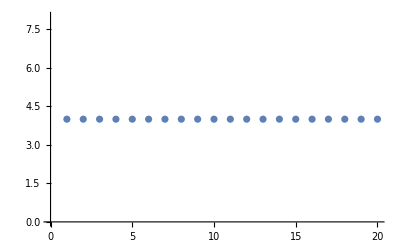

```mathematica
ListPlot[{a11/A11}]
```

```mathematica
a12=Array[a2,3];
A12=Array[A2,3];
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
```

```mathematica
For[i=1,i<3,i++,
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
a12[[i]]=Re[(1/4^6)* Sum[Tr[PauliString2[i1,j1].PauliString2[i3,j3].PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i1,j1].PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2.PauliString2[i4,j4]]*Tr[PauliString2[i3,j3].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2],{i,0,3},{i1,0,3},{i2,0,3},{i3,0,3},{i4,0,3},{j,0,3},{j1,0,3},{j2,0,3},{j3,0,3},{j4,0,3}]];
A12[[i]]=Re[Tr[Q2.KroneckerProduct[kk2†,kk2†,kk2†,kk2†].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].permutationMatrix[Flatten[permdouble[[9]]]]]];
]
a12
A12
```

```mathematica
Re[(1/4^6)* Sum[Tr[PauliString2[i1,j1].PauliString2[i3,j3].PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i1,j1].PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2.PauliString2[i4,j4]]*Tr[PauliString2[i3,j3].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2],{i,0,3},{i1,0,3},{i2,0,3},{i3,0,3},{i4,0,3},{j,0,3},{j1,0,3},{j2,0,3},{j3,0,3},{j4,0,3}]]
```

15.8622

```mathematica
Re[Tr[Q2.KroneckerProduct[kk2†,kk2†,kk2†,kk2†].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].permutationMatrix[Flatten[permdouble[[9]]]]]]
```

0.991385

```mathematica
15.862160074458327/0.9913850046536458
```

16.

```mathematica
PauliString1[i_]:=PauliMatrix[i];
PauliString2[i_,j_]:=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]];
PauliString3[i_,j_,k_]:=KroneckerProduct[SparseArray[PauliMatrix[i]],SparseArray[PauliMatrix[j]],SparseArray[PauliMatrix[k]]];
```

```mathematica
Sum[(Tr[PauliString1[i]]),{i,0,3}]
```

2

```mathematica
Sum[(Tr[PauliString2[i,j]]),{i,0,3},{j,0,3}]
```

4

```mathematica
Sum[(Tr[PauliString3[i,j,k]]),{i,0,3},{j,0,3},{k,0,3}]
```

8

```mathematica
1-2^(1-Log[2,5])
```

3/5

```mathematica
Eigenvalues[FourierMatrix[2]]
```

{-1,1}

```mathematica
Eigenvalues[FourierMatrix[4]]
```

{-1,ⅈ,1,1}

```mathematica
Eigenvalues[FourierMatrix[8]]//N//Chop
```

{-1.,-1.,1.,1.,1.,0.-1. ⅈ,0.+1. ⅈ,0.+1. ⅈ}

```mathematica
Eigenvalues[FourierMatrix[16]]//N//Chop
```

# Alioscia test

## 1 qubit

```mathematica
(* function to generate the pertunations *)
indexToQubitIndices[n_,numQubits_]:=PadLeft[IntegerDigits[n-1,2],numQubits];
permutationMatrix[permutation_]:=With[{numQubits=Length@permutation},SparseArray[{{i_,j_}:>1/;Equal[Permute[indexToQubitIndices[i,numQubits],permutation],indexToQubitIndices[j,numQubits]]},2^numQubits {1,1}]];
```

```mathematica
(* Generated by the 4 Pauli strings on 1 qubit but taken to 4 times replicated space *)
PauliString1[i_]:=PauliMatrix[i];
Q1=(1/4)*Sum[KroneckerProduct[PauliString1[i],PauliString1[i],PauliString1[i],PauliString1[i]],{i,0,3}];

(* list the possible permutations of 1 qubit on 4 times replicated space *)
permsingle=Permutations@{1,2,3,4};

(* total operator reads *)
P1=(1/24)*Sum[permutationMatrix[Flatten[permsingle[[i]]]],{i,1,24}];
```

```mathematica
RU1=RandomVariate[CircularUnitaryMatrixDistribution[2]];
```

```mathematica
RU1//MatrixForm
```

(0.726074+0.13299 ⅈ | -0.287865+0.610134 ⅈ
0.59119+0.325 ⅈ | 0.509773-0.533855 ⅈ)

```mathematica
UnitaryMatrixQ[RU1]
```

True

```mathematica
Tr[ KroneckerProduct[ConjugateTranspose[RU1],ConjugateTranspose[RU1],ConjugateTranspose[RU1],ConjugateTranspose[RU1]].Q1.KroneckerProduct[RU1,RU1,RU1,RU1].P1]
```

2.+1.76364×10^-17 ⅈ

```mathematica
Tr[Q1.P1]
```

2

```mathematica
P1.KroneckerProduct[RU1,RU1,RU1,RU1]-KroneckerProduct[RU1,RU1,RU1,RU1].P1//Chop
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
P1.KroneckerProduct[ConjugateTranspose[RU1],ConjugateTranspose[RU1],ConjugateTranspose[RU1],ConjugateTranspose[RU1]]-KroneckerProduct[ConjugateTranspose[RU1],ConjugateTranspose[RU1],ConjugateTranspose[RU1],ConjugateTranspose[RU1]].P1//Chop
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## 2 qubits

```mathematica
(* Generated by the 16 Pauli strings on 2 qubits but taken to 4 times replicated space *)
PauliString2[i_,j_]:=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]];
Q2=(1/16)*Sum[KroneckerProduct[PauliString2[i,j],PauliString2[i,j],PauliString2[i,j],PauliString2[i,j]],{i,0,3},{j,0,3}];

(* list the possible permutations of 2 qubits on 4 times replicated space *)
permdouble=Permutations@{{1,2},{3,4},{5,6},{7,8}};

(* total operator reads *)
P2=(1/24)*Sum[permutationMatrix[Flatten[permdouble[[i]]]],{i,1,24}];
```

```mathematica
RU2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
```

```mathematica
RU2//MatrixForm
```

(-0.287024+0.1537 ⅈ | 0.0763575+0.214086 ⅈ | 0.693526-0.25843 ⅈ | -0.197722-0.505442 ⅈ
0.262436+0.253796 ⅈ | 0.474471-0.664641 ⅈ | 0.0314744+0.240067 ⅈ | 0.0333854-0.374309 ⅈ
0.40191-0.587535 ⅈ | 0.454963+0.271669 ⅈ | 0.180869+0.183802 ⅈ | -0.374137+0.0774579 ⅈ
0.501491+0.0498543 ⅈ | 0.0212827-0.0147632 ⅈ | 0.444357-0.360088 ⅈ | 0.574845+0.296291 ⅈ)

```mathematica
UnitaryMatrixQ[RU2]
```

True

```mathematica
Tr[ KroneckerProduct[ConjugateTranspose[RU2],ConjugateTranspose[RU2],ConjugateTranspose[RU2],ConjugateTranspose[RU2]].Q2.KroneckerProduct[RU2,RU2,RU2,RU2].P2]
```

5.-8.69745×10^-17 ⅈ

```mathematica
TensorProduct[P1.Q1,P2.Q2]-TensorProduct[Q1.P1,Q2.P2]//TensorReduce
```

(P1.Q1)⊗(P2.Q2)-(Q1.P1)⊗(Q2.P2)

```mathematica
LeviCivitaTensor[3].b.a
```

SparseArray[…].b.a

```mathematica
Cross[a,b,c]
```

a×b×c